```mathematica
g=9.8;
l=0.5;
c=3 10^8;
m=1;
vt=Sqrt[m g/c];
ode1=x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2];
ode2=y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]);
sol=NDSolve[{{ode1,x[0]==0,x'[0]==50},{ode2,y[0]==0,y'[0]==30}},{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

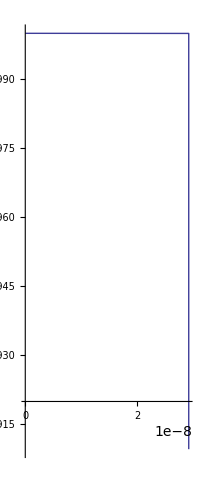

-Graphics-

```mathematica
v=30;
θ=50*π/180;
sol=NDSolve[{ode1,x[0]==0,x'[0]==v Cos[θ],ode2,y[0]==2,y'[0]==v Sin[θ]},{x,y},{t,0,200}];
myplot1=ParametricPlot[{x[t]/.sol[[1]][[1]],y[t]/.sol[[1]][[2]]},{t,0,5},PlotRange->All]
Show[myplot1]
```

```mathematica
Manipulate[Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),{x[0]==0,y[0]==y0},{x'[0]==v Cos[th],y'[0]==v Sin[th]}},{x,y},{t,0,200}]},ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{v Cos[th] t,y0+v Sin[th] t-0.5 g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,150},{0,150}},ImageSize->{500,300}]],{{y0,0,"\!\(\*SubscriptBox[\(y\), \(0\)]\) (m)"},0,200,Appearance->"Labeled"},{{v,10,},10,200,Appearance->"Labeled"},{{vt,10,"\!\(\*SubscriptBox[\(v\), \(terminal\)]\) (m/s)"},10,200,Appearance->"Labeled"},{{th,0.1,"\!\(\*SubscriptBox[\(θ\), \(0\)]\) (rad)"},.1,π/2,Appearance->"Labeled"},{{tf,20,"time (s)"},0.01,20.,Appearance->"Labeled"}]
```